# Tests of Fabbri Data with Phylogeny

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\nathanm\OneDrive\dinosaur research\fabbri et al rebuttal\mathematica for github

```mathematica
CloseKernels[];
LaunchKernels[]
```

{Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local}

```mathematica
<<"phylo for mathematica\\PollyPhylogenetics6.6.m"
```

Phylogenetics for Mathematica 6.6
(c) P. David Polly, 26 November 2022

## General Functions

```mathematica
cleanmatrix[wraw_]:= Map[Drop[#,1]&,Drop[wraw,1]];
```

```mathematica
makenmatrix[w_]:=
Module[{invw,eval,evec,tevec,invtevec,dig,n1,dexp,divnum},
invw = Inverse[w];
{eval,evec} = Eigensystem[invw];
tevec = Transpose[evec];
invtevec = Inverse[tevec];
dig = DiagonalMatrix[Sqrt[eval]];
n1 = tevec.dig.invtevec;
dexp = 1/Length[w];
divnum = Det[n1]^dexp;
n1/divnum
];
```

```mathematica
matrix4lambda[mat_,lamobs_]:=
Module[{dm,nd},
dm = DiagonalMatrix[Diagonal[mat]];
nd = (mat - dm)/lamobs;
{dm,nd}
]
```

```mathematica
matrixsquareroot[mat_]:=
Module[{invw,eval,evec,tevec,invtevec,dig},
{eval,evec} = Eigensystem[mat];
tevec = Transpose[evec];
invtevec = Inverse[tevec];
dig = DiagonalMatrix[Sqrt[eval]];
tevec.dig.invtevec
];
```

## Plot Functions

```mathematica
logticks =  Join[Table[{Log[10^k],10^k},{k,0,3}],Flatten[Table[{Log[j*10^k],""},{k,0,3},{j,2,9,1}],1]];
```

```mathematica
log10ticks = Join[Table[{k,10^k},{k,0,3}],Flatten[Table[{Log[10,j*10^k],""},{k,0,3},{j,2,9,1}],1]];
```

```mathematica
xlines[pt_,armlen_]:= {Line[{pt-{armlen,0},pt+{armlen,0}}],Line[{pt-{0,armlen},pt+{0,armlen}}]};
```

```mathematica
xlines2[pt_,{armlen1_,armlen2_}]:= {Line[{pt-{armlen1,0},pt+{armlen1,0}}],Line[{pt-{0,armlen2},pt+{0,armlen2}}]};
```

```mathematica
topticklabel[min_,max_,lab_]:= {{min,Style[lab,"Arial",12,Bold],0}};
```

```mathematica
mswordsize = 6.5*72;
```

```mathematica
shadeopacity = 0.3;
pointopacity = 0.6;
```

## Phylogenetic tree

### Rib

```mathematica
ribtreeraw = Import["tree_ribs_final.nex","Lines"];
```

```mathematica
ribtreeindex = Map[DeleteCases[#,""]&,StringSplit[ribtreeraw[[5;;179]],Whitespace..|"'"|","]];
```

```mathematica
ribtreenamerules = Map[StringJoin[#[[1]],":"]-> StringJoin[#[[2]],":"]&,ribtreeindex];
```

```mathematica
ribtreess = StringSplit[ribtreeraw[[3]],"tree:"|"[%"];
```

```mathematica
rtt =StringJoin[ ribtreess[[2]],";"];
```

```mathematica
ribtree = StringReplace[ StringDelete[rtt," "],ribtreenamerules];
```

```mathematica
(*DrawNewickTree[ribtree]*)
```

```mathematica
wribraw=PhylogeneticMatrices[ribtree][[1]];
```

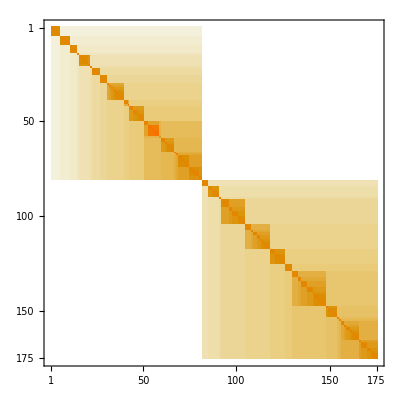

```mathematica
MatrixPlot[cleanmatrix[wribraw]]
```

```mathematica
allnamesinribtree = Drop[wribraw[[1]],1];
```

### Femur

```mathematica
femurtreeraw = Import["tree_femur_final.nex","Lines"];
```

```mathematica
femurtreess =StringSplit[femurtreeraw[[3]],"R]"|";"];
```

```mathematica
femurtree =StringJoin[StringDelete[femurtreess[[2]]," "],";"];
```

```mathematica
wfemurraw=PhylogeneticMatrices[femurtree][[1]];
```

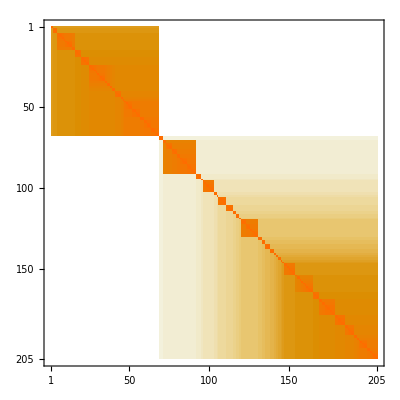

```mathematica
MatrixPlot[cleanmatrix[wfemurraw]]
```

```mathematica
allnamesinfemurtree = Drop[wfemurraw[[1]],1];
```

## Data with phylogeny

```mathematica
phyloadjustpts[{class1_,class2_,class3_}, tree_,plam_]:=
Module[{rawd,alldata,lens,indicator,names,namebyclass,datapts,databyclass,dtree,wmatraw,namesfromtree,wmat,
wmatdia,wmatoffdia,wwl,nwl,datpts,datanames,nameorder,indicatoradj,datptsinorder,datadj,datadjbyclass,namesinorderclass},
rawd = {class1,class2,class3};
alldata = Flatten[rawd,1];
lens = Map[Length,rawd];
indicator ={Join[Table[1,{lens[[1]]}],Table[0,{lens[[2]]}],Table[0,{lens[[3]]}]],Join[Table[0,{lens[[1]]}],Table[1,{lens[[2]]}],Table[0,{lens[[3]]}]],Join[Table[0,{lens[[1]]}],Table[0,{lens[[2]]}],Table[1,{lens[[3]]}]]};
names = alldata[[All,1]];
namebyclass = Table[Pick[names,indicator[[i]],1],{i,1,3}];
datapts = alldata[[All,{1,11,9}]];
databyclass = Table[Pick[datapts,indicator[[i]],1],{i,1,3}];
dtree = PruneTree[Flatten[databyclass[[All,All,1]]],tree];
wmatraw = PhylogeneticMatrices[dtree][[1]];
namesfromtree = Drop[wmatraw[[1]],1];
wmat = cleanmatrix[wmatraw];
(*nmat = makenmatrix[wmat];*)
{wmatdia, wmatoffdia}= matrix4lambda[wmat,1];
wwl = wmatdia + plam*wmatoffdia;
nwl = makenmatrix[wwl];
datpts= Flatten[databyclass[[All, All,{2,3}]],1];
datanames =  Flatten[databyclass[[All,All,1]],1];
nameorder = FindPermutation[datanames,namesfromtree];
indicatoradj = Map[Permute[#,nameorder]&,indicator];
datptsinorder = Permute[datpts,nameorder];
datadj = nwl.datptsinorder;
datadjbyclass = Table[Pick[datadj,indicatoradj[[i]],1],{i,1,3}];
namesinorderclass =  Table[Pick[namesfromtree,indicatoradj[[i]],1],{i,1,3}];
{datadjbyclass,namesinorderclass}
];
```

### Femur (new)

```mathematica
spinonames2 = {"Su","Ba","Sp"};
```

```mathematica
femurallraw  = Import["femur compactness all.csv"];
```

```mathematica
{Range[Length[femurallraw[[1]]]],femurallraw[[1]]}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
taxa | Reference | Specimen | Type of data | AFA | ALA | FAD | LAD | Global compactness | MD (mm) | MD log | Flying | Diving | finest.category | diving.or.not

```mathematica
femurallraw1 = Drop[femurallraw,1];
```

```mathematica
femurf0raw = Pick[femurallraw1,femurallraw1[[All,12]],0];
```

```mathematica
namesnotintree = Complement[femurf0raw[[All,1]],allnamesinfemurtree]
```

{Rhinoceros_unicornis}

```mathematica
badpos = Flatten[Map[Position[femurf0raw[[All,1]],#]&,namesnotintree],1]
```

{{112}}

```mathematica
femurf0raw1 = Delete[femurf0raw,badpos];
```

```mathematica
femurf0d0raw =  Pick[femurf0raw1,femurf0raw1[[All,13]],0];
```

```mathematica
femurf0d2raw =  Pick[femurf0raw1,femurf0raw1[[All,13]],2];
```

```mathematica
femurdinos = Pick[femurf0raw1,femurf0raw1[[All,13]],"UNKNOWN"];
```

```mathematica
fwdinosadj = phyloadjustpts[{femurf0d0raw,femurf0d2raw,femurdinos}, femurtree,0.06];
```

```mathematica
Position[fwdinosadj[[2,3]],"Spinosaurus_"]
```

{{17}}

```mathematica
Position[fwdinosadj[[2,3]],"Baryonyx"]
```

{{15}}

```mathematica
Position[fwdinosadj[[2,3]],"Suchomimus"]
```

{{16}}

```mathematica
spinonames2
```

{Su,Ba,Sp}

```mathematica
femurspinoadjpts = fwdinosadj[[1,3,{16,15,17}]]
```

{{1.47478,0.433565},{1.58328,0.631825},{1.30225,0.72605}}

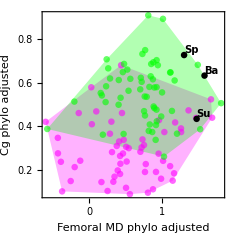

```mathematica
femuradjplot = Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,2]]]}},
Table[{Black,PointSize[.02],Point[femurspinoadjpts[[k]]]},{k,1,Length[spinonames2]}],
Table[Text[Style[spinonames2[[k]],Black,10,Italic,Bold],femurspinoadjpts[[k]],{-1,-1}],{k,1,Length[spinonames2]}],
(*Text[Style["F0D2",10,"Arial",Bold,Italic],{Log[2],0.88},{0,0}],
Text[Style["F0D0",10,"Arial",Bold,Italic],{Log[50],0.45},{0,0}]*)
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},FrameLabel-> {"Femoral MD phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

```mathematica
fm1 = Mean[fwdinosadj[[1,1]]]
```

{0.539852,0.29243}

```mathematica
fm2=Mean[fwdinosadj[[1,2]]]
```

{0.732264,0.555206}

```mathematica
femurrange =Map[MinMax,Transpose[Join[fwdinosadj[[1,1]],fwdinosadj[[1,2]]]]]
```

{{-0.602994,1.81182},{0.0883727,0.908312}}

```mathematica
frrat =(femurrange[[2,2]]-femurrange[[2,1]])/(femurrange[[1,2]]-femurrange[[1,1]])
```

0.339545

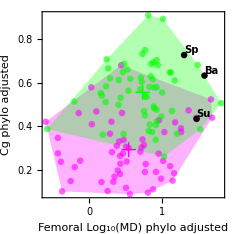

```mathematica
femuradjplot2 = Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,2]]]}},
{Magenta,Thick, xlines2[fm1,0.1*{1,frrat}]},
{Green,Thick, xlines2[fm2,0.1*{1,frrat}]},
Table[{Black,PointSize[.02],Point[femurspinoadjpts[[k]]]},{k,1,Length[spinonames2]}],
Table[Text[Style[spinonames2[[k]],Black,10,Italic,Bold],femurspinoadjpts[[k]],{-1,-1}],{k,1,Length[spinonames2]}],
(*Text[Style["F0D2",10,"Arial",Bold,Italic],{Log[2],0.88},{0,0}],
Text[Style["F0D0",10,"Arial",Bold,Italic],{Log[50],0.45},{0,0}]*)
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},FrameLabel-> {"Femoral Log_10(MD) phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

### Rib (new)

```mathematica
ribspinonames2 = {"Ba","Sp"};
```

```mathematica
riballraw  = Import["ribs compactness all.csv"];
```

```mathematica
riballraw1 = Drop[riballraw,1];
```

```mathematica
ribf0raw = Pick[riballraw1,riballraw1[[All,12]],0];
```

```mathematica
namesnotinribtree = Complement[ribf0raw[[All,1]],allnamesinribtree]
```

{Capra_aegagrus}

```mathematica
ribbadpos = Flatten[Map[Position[ribf0raw[[All,1]],#]&,namesnotinribtree],1]
```

{{76}}

```mathematica
ribf0raw1 = Delete[ribf0raw,ribbadpos];
```

```mathematica
ribf0d0raw =  Pick[ribf0raw1,ribf0raw1[[All,13]],0];
```

```mathematica
ribf0d2raw =  Pick[ribf0raw1,ribf0raw1[[All,13]],2];
```

```mathematica
ribdinos = Pick[ribf0raw1,ribf0raw1[[All,13]],"UNKNOWN"];
```

```mathematica
ribdinos
```

{{Lourinhanosaurus,Waskow & Mateus (2017),ML 370,,11,12,155.7,145,0.631,11.3,1.05308,0,UNKNOWN,none,0},{Saltriovenator,Dal Sasso et al. (2018),MSNM V3664,,4,5,196.5,189.6,0.704,21.3,1.32838,0,UNKNOWN,none,0},{Baryonyx,This study,BMNH 9951,Thin section,13,13,129.4,127,0.921,42.2,1.62531,0,UNKNOWN,UNKNOWN,UNKNOWN},{Spinosaurus,This study,FSAC-KK 11888,Thin section,14,14,100.5,93.9,0.931,35.1,1.54531,0,UNKNOWN,UNKNOWN,UNKNOWN},{Charcarodontosaurid,Cullen et al. (2020),MMCh PV 65,,14,15,100.5,89.8,0.805,25.5,1.40654,0,UNKNOWN,none,0},{Alamosaurus,Woodward (2005),HW-R2,,18,18,72.1,66,0.523,82.6,1.91698,0,UNKNOWN,none,0},{Plateosaurus,Klein & Sander (),SMNS F 29,Thin section,3,3,227,208.5,0.513,17.1,1.233,0,UNKNOWN,none,0},{Spinophorosaurus_nigerensis,Houssaye et al. (2016),Ni 5.40-7ax,,7,8,170.3,166.1,0.68,64.3,1.80821,0,UNKNOWN,none,0},{Apatosaurus_sp,Houssaye et al. (2016),BYU 145,,11,12,155.7,145,0.8,52.3,1.7185,0,UNKNOWN,none,0},{Diplodocus_sp,Houssaye et al. (2016),CMC 9932 ,,11,12,155.7,145,0.85,35,1.54407,0,UNKNOWN,none,0},{Brachiosaurus_sp,Houssaye et al. (2016),FMNH 25107,,11,12,155.7,145,0.84,95,1.97772,0,UNKNOWN,none,0},{Miragaia_longicollum,Houssaye et al. (2016),ML 433A ,,12,12,152.1,145,0.79,35,1.54407,0,UNKNOWN,none,0}}

```mathematica
rwdinosadj = phyloadjustpts[{ribf0d0raw,ribf0d2raw,ribdinos}, ribtree,0.07];
```

```mathematica
Position[rwdinosadj[[2,3]],"Spinosaurus"]
```

{{9}}

```mathematica
Position[rwdinosadj[[2,3]],"Baryonyx"]
```

{{8}}

```mathematica
Position[rwdinosadj[[2,3]],"Suchomimus"]
```

{}

```mathematica
ribspinonames2
```

{Ba,Sp}

```mathematica
ribspinoadjpts = rwdinosadj[[1,3,{8,9}]]
```

{{1.38577,0.754878},{1.30351,0.76516}}

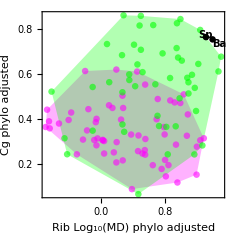

```mathematica
ribadjplot =Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,2]]]}},
Table[{Black,PointSize[.02],Point[ribspinoadjpts[[k]]]},{k,1,Length[ribspinonames2]}],
Table[Text[Style[ribspinonames2[[k]],Black,10,Italic,Bold],ribspinoadjpts[[k]]+{{0,0},{0,.01}}[[k]],{{-1,1},{0,-1}}[[k]]],{k,1,Length[ribspinonames2]}]
(*Text[Style["F0D2",10,"Arial",Bold,Italic],{Log[2],0.88},{0,0}],
Text[Style["F0D0",10,"Arial",Bold,Italic],{Log[50],0.45},{0,0}]*)
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},FrameLabel-> {"Rib Log_10(MD) phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

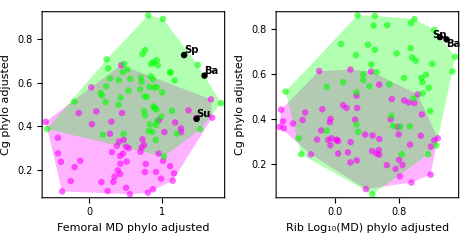

```mathematica
fig1xxplot = GraphicsGrid[{{femuradjplot,ribadjplot}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
rm1 = Mean[rwdinosadj[[1,1]]]
```

{0.341513,0.343684}

```mathematica
rm2=Mean[rwdinosadj[[1,2]]]
```

{0.643651,0.557606}

```mathematica
ribrange =Map[MinMax,Transpose[Join[rwdinosadj[[1,1]],rwdinosadj[[1,2]]]]]
```

{{-0.6892,1.49241},{0.0655582,0.862263}}

```mathematica
rrrat =(ribrange[[2,2]]-ribrange[[2,1]])/(ribrange[[1,2]]-ribrange[[1,1]])
```

0.365191

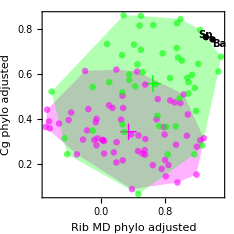

```mathematica
ribadjplot2 =Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,2]]]}},
{Magenta,Thick, xlines2[rm1,0.1*{1,rrrat}]},
{Green,Thick, xlines2[rm2,0.1*{1,rrrat}]},
Table[{Black,PointSize[.02],Point[ribspinoadjpts[[k]]]},{k,1,Length[ribspinonames2]}],
Table[Text[Style[ribspinonames2[[k]],Black,10,Italic,Bold],ribspinoadjpts[[k]]+{{0,0},{0,.01}}[[k]],{{-1,1},{0,-1}}[[k]]],{k,1,Length[ribspinonames2]}],
(*Text[Style["F0D2",10,"Arial",Bold,Italic],{Log[2],0.88},{0,0}],
Text[Style["F0D0",10,"Arial",Bold,Italic],{Log[50],0.45},{0,0}]*)
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},FrameLabel-> {"Rib MD phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

```mathematica
Sqrt[(rm1-rm2).(rm1-rm2)]
```

0.370203

```mathematica
StandardDeviation[Join[Map[# -rm1&,rwdinosadj[[1,1]]],Map[# -rm1&,rwdinosadj[[1,2]]]]]
```

{0.532597,0.186505}

```mathematica
femurf0d0andf0d2 = Join[femurf0d0raw,femurf0d2raw];
indicatorf0d0andf0d2 = {Join[Table[1,{Length[femurf0d0raw]}],Table[0,{Length[femurf0d2raw]}]],
Join[Table[0,{Length[femurf0d0raw]}],Table[1,{Length[femurf0d2raw]}]]};
femurf0d0andf0d2names =femurf0d0andf0d2[[All,1]];
femurnamesbyclass = Table[Pick[femurf0d0andf0d2names,indicatorf0d0andf0d2[[i]],1],{i,1,2}];
femurdata = femurf0d0andf0d2[[All,{1,11,9}]];
femurdatabyclass = Table[Pick[femurdata,indicatorf0d0andf0d2[[i]],1],{i,1,2}];
```

```mathematica
femursets2 = {femurdatabyclass[[1,All,{2,3}]],femurdatabyclass[[2,All,{2,3}]],fwdinosadj[[1,1]],fwdinosadj[[1,2]]};
```

```mathematica
DistributeDefinitions[femursets2,fwdinosadj]
```

{}

```mathematica
femursetnames2 = {"F0D0","F0D2","F0D0: lam = 0.06","F0D2, lam = 0.06"};
```

```mathematica
ribf0d0andf0d2 = Join[ribf0d0raw,ribf0d2raw];
indicatorf0d0andf0d2rib = {Join[Table[1,{Length[ribf0d0raw]}],Table[0,{Length[ribf0d2raw]}]],
Join[Table[0,{Length[ribf0d0raw]}],Table[1,{Length[ribf0d2raw]}]]};
ribf0d0andf0d2names =ribf0d0andf0d2[[All,1]];
ribdata = ribf0d0andf0d2[[All,{1,11,9}]];
ribnamesbyclass = Table[Pick[ribf0d0andf0d2names,indicatorf0d0andf0d2rib[[i]],1],{i,1,2}];
ribdatabyclass = Table[Pick[ribdata,indicatorf0d0andf0d2rib[[i]],1],{i,1,2}];
```

```mathematica
ribsets2 = {ribdatabyclass[[1,All,{2,3}]],ribdatabyclass[[2,All,{2,3}]],rwdinosadj[[1,1]],rwdinosadj[[1,2]]};
```

```mathematica
DistributeDefinitions[ribsets2]
```

{}

```mathematica
ribsetnames2 = {"F0D0","F0D2","F0D0: lam = 0.07","F0D2, lam = 0.07"};
```

## Discriminant data

From ds1 and ds2, F0D0 vs F0D2

```mathematica
fdiscbyclass ={{0.1673563028097216,0.439926183927034,-1.922731437354999,-1.151356101412108,0.3103074572377685,0.3298469093560582,-0.2513593877276705,-0.6220310811999185,-0.7157254918736934,-0.11370478740041604,-0.37566528404595806,-0.6216804824059051,-1.4247096759261022,-0.4120967153406295,-1.330631608604355,-0.43643825043325046,1.0602535812969835,0.5903143402119944,0.24178258527753496,-1.938339168449175,0.47357317606317323,-0.9127025111201281,-0.9584277440194704,-0.5102958776173588,-0.45223540577456156,-2.0497357616817804,-1.2011809897260821,0.014714806550293703,0.32194510573705115,-0.7547239193802845,-1.8192414939178305,-1.1969627926045987,-1.47848206122433,-1.9670409186559916,-1.2517454613845187,0.4864184982305844,0.6952716317467577,-1.1991454563454746,0.7365638243331556,-1.898246770038551,1.365024232051833,0.6513433711161859,0.6845878908988104,-0.0787801744254809,-0.26508296833520795,-2.244030027181247,0.6025058647406464,-1.1383831607491415,-1.7338553252832363,-2.2382991011757127,-2.737777403912854,-0.9668593422477891,-1.8606351910459344,-1.5719832616973983,-1.3759868599616372,-2.161040212283875,-2.790746708296052,-2.3409338495817322},{1.1333705761359925,0.4362942913800992,-0.14180218621924073,0.06608943569184232,1.48796210953157,1.192639451224252,0.2562967966130752,0.22485025319297638,2.23410867330532,2.1945846205916992,0.9832501540630858,-0.09527404859899781,1.3293471187183672,1.865920742825315,2.371459051220367,1.5995892647814376,0.5561164234033735,0.5719080383724999,0.272403078640695,1.113397432730644,1.0674385705359117,-0.8561903638693493,1.3232736964023015,1.9415715444856996,2.0518579770107546,0.3298806612936043,-0.6762973538406594,0.8789281010197433,1.7165774115790045,1.5033617882624701,0.709481742110417,1.183292648730531,1.771329497596365,1.876884717880723,0.9308524778430529,0.09017968064208037,1.8548493586786774,1.236321597846418,1.5305776536467877,0.7635471734916577,0.5963801237757385,0.17862601815589507,-0.1263786339544307,1.5912761805880966,1.4724755708274389,1.2126885027534324,0.3689667217355734,-0.5197417821301203,2.52029425801159,1.4856040177097716,1.5165981895632832,0.8555166381637392,2.1133671954687037,-0.6809285661869857,1.406089447936062,1.762796693563474,1.318687345915038,0.9619810936830009,-0.25999344579305006}};
```

```mathematica
fdiscbyclasscentered ={{0.9844124535979092,1.2569823347152216,-1.1056752865668114,-0.3342999506239205,1.1273636080259561,1.1469030601442458,0.5656967630605171,0.19502506958826915,0.10133065891449422,0.7033513633877716,0.44139086674222955,0.19537566838228249,-0.6076535251379146,0.4049594354475581,-0.5135754578161674,0.38061790035493714,1.877309732085171,1.407370491000182,1.0588387360657225,-1.1212830176609874,1.290629326851361,-0.09564636033194052,-0.1413715932312828,0.30676027317082877,0.36482074501362605,-1.2326796108935927,-0.3841248389378945,0.8317709573384813,1.1390012565252388,0.062332231407903116,-1.0021853431296428,-0.3799066418164111,-0.6614259104361423,-1.149984767867804,-0.4346893105963311,1.303474649018772,1.5123277825349453,-0.38208930555728704,1.553619975121343,-1.0811906192503633,2.1820803828400206,1.4683995219043735,1.501644041686998,0.7382759763627067,0.5519731824529797,-1.4269738763930593,1.419562015528834,-0.32132700996095387,-0.9167991744950487,-1.421242950387525,-1.9207212531246665,-0.14980319145960153,-1.0435790402577467,-0.7549271109092107,-0.5589307091734496,-1.3439840614956875,-1.9736905575078643,-1.5238776987935445},{0.33016283468319785,-0.36691345007269544,-0.9450099276720354,-0.7371183057609523,0.6847543680787754,0.38943170977145736,-0.5469109448397194,-0.5783574882598183,1.4309009318525252,1.3913768791389045,0.1800424126102912,-0.8984817900517924,0.5261393772655726,1.0627130013725203,1.568251309767572,0.796381523328643,-0.24709131804942108,-0.23129970308029468,-0.5308046628120996,0.31018969127784934,0.2642308290831171,-1.6593981053221438,0.5200659549495069,1.138363803032905,1.2486502355579598,-0.4733270801591903,-1.479505095293454,0.07572035956694867,0.9133696701262098,0.7001540468096755,-0.09372599934237758,0.3800849072777365,0.9681217561435703,1.0736769764279286,0.1276447363902583,-0.7130280608107142,1.051641617225883,0.4331138563936233,0.727369912193993,-0.03966056796113693,-0.20682761767705615,-0.6245817232968995,-0.9295863754072253,0.788068439135302,0.6692678293746442,0.4094807613006378,-0.43424101971722123,-1.322949523582915,1.7170865165587954,0.682396276256977,0.7133904481104886,0.05230889671094463,1.310159454015909,-1.4841363076397802,0.6028817064832673,0.9595889521106794,0.5154796044622433,0.15877335223020628,-1.0632011872458447}};
```

```mathematica
rdiscbyclass ={{0.12204587081728537,-0.5739930544982649,-0.5900342311590894,-0.3018240027478353,-0.2835006963022949,-0.8210074279506078,-0.8546244967160526,-1.7597817021333166,-1.7420425998048,-0.7423678337326847,0.08320491022856859,-0.4682045251723951,0.2666800247220776,1.1258051284680501,-0.9943180404788778,-1.8186218884350935,-1.6398474961372806,-1.2508837571792166,-0.12618715454034327,-1.3809928773783462,-1.5100798587781712,-0.7666470256603561,-0.9927805722774942,-0.20913650929760105,-0.5131266023361698,-0.9586676472139953,-0.9904587121678166,-0.9691686274833442,-0.3008472337398761,-0.8909682803596091,-0.741672038778845,-1.3076615235743574,-0.8228865278976311,-1.4412592567942055,1.3702976307438428,0.574817928912277,-0.7017311340763359,-0.8835323136833254,-0.3814876915376749,-0.19424616710238937,-0.021643334746340705,0.1978580513888253,1.6876851963572381,0.9631493981840086,-0.25656413849427645,-1.0376386349061768,-1.446221650746315,-2.224213841031467,0.40732523657883707,-0.15291240514812984,-1.5736584049139393,-0.21107209328421073,-0.7844614602772637,-0.6330735555169776,-1.284501639215647,-0.8708997556342352,-0.35722331085385967,-0.49513620472691305,-1.2996520747816045,-1.5651728610515672,-0.2305225480549704,-1.0665999822802303},{0.44680383615161673,1.6614564415437572,1.9396349544125329,1.524537782804097,1.8909667675352548,-0.18332006170102727,2.155001719595267,1.929345000887594,0.39033353754596817,1.2291109590397116,1.3610375998799438,0.8478582101877324,1.8966158234286077,1.1518102121086402,0.8063647599277557,0.8289609432378396,-0.25935455055636625,1.4175532731549585,-0.49309028997738436,1.5116872548998335,-1.251200675269033,0.9486658365558046,1.2767937299337746,-1.8196017278650238,0.41832995382281674,0.4051156958368924,2.5199501653750045,-2.383526214358447,1.6989347146709093,1.3598501300588777,-0.3565893623856996,-0.7274999617809207,0.6420862780456628,0.35710679848481963,1.2500926924254288,2.619998919006877,2.3050569529218166,-0.3743305435882448,0.13873516406164307,0.5419431261569555,1.638916121139876,1.9002878813346133,1.90630975389426,2.5941107892257764,3.0880176242944466,1.6966255982414624,2.023625829234531,-0.4044471477303858,2.6421614146416466}};
```

```mathematica
rdiscbyclasscentered ={{0.8113131024627183,0.11527417714716803,0.09923300048634354,0.38744322889759764,0.405766535343138,-0.13174019630517486,-0.16535726507061965,-1.0705144704878837,-1.052775368159367,-0.05310060208725176,0.7724721418740015,0.22106270647303783,0.9559472563675104,1.815072360113483,-0.30505080883344493,-1.1293546567896606,-0.9505802644918477,-0.5616165255337837,0.5630800771050897,-0.6917256457329133,-0.8208126271327383,-0.07737979401492323,-0.30351334063206126,0.48013072234783183,0.1761406293092631,-0.2694004155685624,-0.30119148052238365,-0.2799013958379113,0.3884199979055568,-0.20170104871417616,-0.05240480713341211,-0.6183942919289245,-0.13361929625219815,-0.7519920251487726,2.0595648623892755,1.26408516055771,-0.012463902430903007,-0.1942650820378925,0.307779540107758,0.4950210645430435,0.6676238968990922,0.8871252830342582,2.376952428002671,1.6524166298294416,0.43270309315115646,-0.3483714032607439,-0.7569544191008821,-1.534946609386034,1.09659246822427,0.536354826497303,-0.8843911732685064,0.4781951383612222,-0.0951942286318308,0.05619367612845527,-0.5952344075702141,-0.18163252398880225,0.33204392079157324,0.19413102691851986,-0.6103848431361716,-0.8759056294061343,0.4587446835904625,-0.37733275063479743},{-0.42533021205280847,0.789322393339332,1.0675009062081076,0.6524037345996717,1.0188327193308298,-1.0554541099054524,1.2828676713908416,1.0572109526831688,-0.481800510658457,0.3569769108352864,0.4889035516755186,-0.024275838016692752,1.0244817752241824,0.279676163904215,-0.0657692882766695,-0.04317310496658555,-1.1314885987607914,0.5454192249505333,-1.3652243381818097,0.6395532066954083,-2.1233347234734583,0.07653178835137942,0.4046596817293494,-2.691735776069449,-0.45380409438160846,-0.4670183523675328,1.6478161171705792,-3.255660262562872,0.8268006664664841,0.4877160818544525,-1.2287234105901248,-1.5996340099853459,-0.23004777015876243,-0.5150272497196056,0.37795864422100356,1.7478648708024518,1.4329229047173913,-1.24646459179267,-0.7333988841427821,-0.3301909220474697,0.7667820729354508,1.028153833130188,1.0341757056898349,1.7219767410213511,2.2158835760900213,0.8244915500370372,1.1514917810301055,-1.276581195934811,1.7700273664372213}};
```

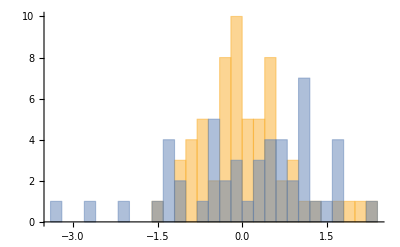

```mathematica
Histogram[rdiscbyclasscentered,20]
```

```mathematica
ribm = Mean[Flatten[rdiscbyclasscentered]]
```

0.0907382

```mathematica
femurmeans = Map[ Mean,fdiscbyclass]
```

{-0.74654,0.994145}

```mathematica
ribmeans = Map[ Mean,rdiscbyclass]
```

{-0.623176,0.994058}

```mathematica
ribsd = StandardDeviation[Flatten[rdiscbyclasscentered]]
```

0.978469

```mathematica
ribdos= (ribmeans[[2]]-ribmeans[[1]])/(ribsd)
```

1.65282

```mathematica
Erfc[(ribmeans[[2]]-ribmeans[[1]])/(Sqrt[2]ribsd)]/2
```

0.0491837

```mathematica
femursd = StandardDeviation[Flatten[fdiscbyclasscentered]]
```

0.944911

```mathematica
femurdos= (femurmeans[[2]]-femurmeans[[1]])/(femursd)
```

1.84217

```mathematica
femurseparatesd = Map[StandardDeviation, fdiscbyclasscentered]
```

{1.05333,0.829476}

```mathematica
eqn3err[dos_]:= 0.5Erfc[dos/Sqrt[2]];
```

```mathematica
eqn7acc[dos_]:= 0.5(2-Erfc[dos/Sqrt[2]]);
```

```mathematica
eqn7acc[femurdos]
```

0.967275

```mathematica
prand[eqn7acc[femurdos]]
```

prand[0.967275]

```mathematica
eqn3err[femurdos]
```

0.0327254

## Hopkins Statistic

This statistic is based on the difference between the distance from a real point to its nearest neighbor, U, and the distance from a randomly chosen point within the data space to the nearest real data point W

```mathematica
(*dist[p1_,p2_]:= Norm[p1-p2];*)
```

```mathematica
dist[p1_,p2_]:= Sqrt[(p1-p2).(p1-p2)];
```

```mathematica
Clear[hopkins,hopkinsch];
hopkins[pts_,frac_]:=
Module[{npts,ranges,randpts,ws,samp,nsamp,us,wsum,usum},
npts = Length[pts];
nsamp = Ceiling[npts*frac];
samp = RandomSample[pts,nsamp];
ranges = Map[MinMax,Transpose[samp]];
randpts = Transpose[Map[RandomReal[#,nsamp]&,ranges]];
ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us= Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
usum/(wsum+usum)
];
```

```mathematica
hopkinsn[pts_,frac_,trials_]:=
Module[{npts,ranges,randpts,ws,samp,nsamp,us,wsum,usum,i,results},
npts = Length[pts];
nsamp = Ceiling[npts*frac];
results = Table[0,{trials}];
For[i=1,i<trials,i++,
samp = RandomSample[pts,nsamp];
ranges = Map[MinMax,Transpose[samp]];
randpts = Transpose[Map[RandomReal[#,nsamp]&,ranges]];
ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us= Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
results[[i]] = usum/(wsum+usum)
];
Median[results]
];
```

```mathematica
lawsonjurs[pts_,frac_]:=
Module[{npts,ranges,randpts,ws,samp,nsamp,us,wsum,usum,xsel,ysel,rangef,xsandys},
npts = Length[pts];
nsamp = Ceiling[npts*frac];
samp = RandomSample[pts,nsamp];
ranges = Map[MinMax,Transpose[samp]];
xsandys = Transpose[pts];
xsel = Cases[xsandys[[1]],a_/;ranges[[1,1]]<= a <= ranges[[1,2]]];
ysel = Cases[xsandys[[2]],a_/;ranges[[2,1]]<= a <= ranges[[2,2]]];
randpts = Transpose[{RandomChoice[xsel,nsamp],RandomSample[ysel,nsamp]}];
ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us = Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
usum/(wsum+usum)
];
```

```mathematica
hopkinschnew[pts_,frac_]:=
Module[{npts,range,randpts,ws,samp,nsamp,us,wsum,usum,reg,},
npts = Length[pts];
nsamp = Max[3,Ceiling[npts*frac]];
samp = RandomSample[pts,nsamp];
reg = ConvexHullRegion[samp];
randpts = RandomPoint[reg,nsamp];
ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us = Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
usum/(wsum+usum)
];
```

```mathematica
hopkinsch[pts_,frac_]:=
Module[{npts,range,randpts,ws,samp,nsamp,us,wsum,usum,reg,regarea,boxarea,arearat,rmemf, rawrandpts,rawrandpts2,extracount,newpts,rawrand2,inregrandpts, inreglen,
missing,x2,newraw,newptslen},
npts = Length[pts];
nsamp = Max[3,Ceiling[npts*frac]];
samp = RandomSample[pts,nsamp];
range = Map[MinMax,Transpose[samp]];
reg = ConvexHullRegion[samp];
regarea = Area[reg];
boxarea = (range[[1,2]]-range[[1,1]])*(range[[2,2]]-range[[2,1]]);
arearat = 2*(boxarea/regarea);
extracount = Ceiling[nsamp*arearat];
rmemf = RegionMember[reg];
rawrandpts = Transpose[Map[RandomReal[#,extracount]&,range]];
inregrandpts = Select[rawrandpts,rmemf];
inreglen =  Length[inregrandpts];
missing = Max[0,nsamp-inreglen];
While[missing >0,
x2 = Max[Ceiling[missing*arearat],2*missing];
newraw =  Transpose[Map[RandomReal[#,x2]&,range]];
newpts = Select[ newraw,rmemf];
newptslen = Length[newpts];
inregrandpts = Join[inregrandpts,newpts];
missing =  Max[0,missing-newptslen];
];
If[Length[inregrandpts] == nsamp,
randpts = inregrandpts;
,
randpts = RandomSample[inregrandpts,nsamp];
];

ws =  Map[RankedMin[#,2]&,Outer[dist[#1,#2]&,samp,samp,1]];
us = Map[Min,Outer[dist[#1,#2]&,randpts,samp,1]];
wsum =Total[ws];
usum = Total[us];
usum/(wsum+usum)
];
```

```mathematica
makechrands[ptlist_]:=
Module[{npts,reg},
npts = Length[ptlist];
reg = ConvexHullRegion[ptlist];
RandomPoint[reg,npts]
];
```

```mathematica
makechrandsold[ptlist_]:=
Module[{npts,range,randpts,ws,samp,nsamp,us,wsum,usum,reg,regarea,boxarea,arearat,rmemf, rawrandpts,rawrandpts2,extracount,newpts,rawrand2,inregrandpts, inreglen,
missing,x2,newraw,newptslen},

nsamp = Length[ptlist];
range = Map[MinMax,Transpose[ptlist]];
reg = ConvexHullRegion[ptlist];
regarea = Area[reg];
boxarea = (range[[1,2]]-range[[1,1]])*(range[[2,2]]-range[[2,1]]);
arearat = 1.2*(boxarea/regarea);
extracount = Ceiling[nsamp*arearat];
rmemf = RegionMember[reg];
rawrandpts = Transpose[Map[RandomReal[#,extracount]&,range]];
inregrandpts = Select[rawrandpts,rmemf];
inreglen =  Length[inregrandpts];
missing = Max[0,nsamp-inreglen];
While[missing >0,
x2 = Max[Ceiling[missing*arearat],2*missing];
newraw =  Transpose[Map[RandomReal[#,x2]&,range]];
newpts = Select[ newraw,rmemf];
newptslen = Length[newpts];
inregrandpts = Join[inregrandpts,newpts];
missing =  Max[0,missing-newptslen];
];
If[Length[inregrandpts] == nsamp,
randpts = inregrandpts;
,
randpts = RandomSample[inregrandpts,nsamp];
];
randpts
];
```

```mathematica
hfrac = 0.2;
```

```mathematica
twosided[cdf_]:= 2*Min[cdf,1-cdf];
```

```mathematica
hoppvalue[dist_,x_]:= 
Module[{cdfv},
cdfv = CDF[dist,x];
2*Min[cdfv,1-cdfv]
];
```

```mathematica
makerandpts[count_,ranges_]:= Transpose[Map[RandomReal[#,count]&,ranges]];
```

```mathematica
unifpts[rang_,nn_,trials_]:=Table[ Transpose[Map[RandomReal[#,nn]&,rang]],{trials}];
```

```mathematica
Clear[hopkinstest]
```

```mathematica
hopkinstest[data_,hopfun_,frac_,nperset_,nsets_,ntrials_]:=
Module[{nulltrials,hs},
nulltrials = Flatten[ParallelTable[With[{testd = makechrandsold[data]},Table[hopfun[testd,frac],{nperset}]],{nsets}]];
hs = Mean[ParallelTable[hopfun[data,frac],{ntrials}]];
{hs,hoppvalue[EmpiricalDistribution[nulltrials],hs]}
];
```

```mathematica
DistributeDefinitions[makechrands,hoppvalue,hfrac,hopkinsch,hopkinschnew,lawsonjurs,hopkinsn,hopkins,dist]
```

{makechrands,hoppvalue,hfrac,hopkinsch,dist,hopkinschnew,lawsonjurs,hopkinsn,hopkins}

## Running Hopkins statistic tests

#### Hopkins null distribution

```mathematica
flens = Map[Length,femursets2]
```

{58,59,58,59}

```mathematica
rlens=Map[Length,ribsets2]
```

{62,49,62,49}

```mathematica
fptranges = Map[Map[MinMax,Transpose[#]]&,femursets2]
```

{{{-0.0357404,2.23553},{0.353,0.855}},{{-0.0136762,2.21864},{0.596,0.989}},{{-0.602994,1.68822},{0.0883727,0.679518}},{{-0.580445,1.81182},{0.260257,0.908312}}}

```mathematica
rptranges = Map[Map[MinMax,Transpose[#]]&,ribsets2]
```

{{{-0.378201,1.7439},{0.451,0.857}},{{-0.305395,1.89098},{0.436,0.998}},{{-0.6892,1.2773},{0.0879499,0.620511}},{{-0.615636,1.49241},{0.0655582,0.862263}}}

```mathematica
DistributeDefinitions[makerandpts,flens,fptranges,rlens,rptranges,femursets2,ribsets2]
```

{makerandpts,flens,fptranges,rlens,rptranges}

```mathematica
AbsoluteTiming[testtrials1 =  Flatten[ParallelTable[With[{testd = makechrandsold[femursets2[[1]]]},Table[hopkinsch[testd,hfrac],{100}]],{100}]];]
```

{13.196,Null}

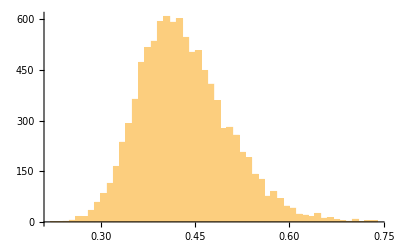

```mathematica
Histogram[testtrials1,{0.01}]
```

```mathematica
AbsoluteTiming[testtrials2 =   Flatten[ParallelTable[With[{testd = makechrandsold[femursets2[[1]]]},Table[hopkinsch[testd,hfrac],{10}]],{100}]];]
```

{1.29081,Null}

```mathematica
AbsoluteTiming[testtrials3 =   Flatten[ParallelTable[With[{testd = makechrandsold[femursets2[[1]]]},Table[hopkinsch[testd,hfrac],{20}]],{100}]];]
```

{2.4481,Null}

```mathematica
AbsoluteTiming[testtrials4=   Flatten[ParallelTable[With[{testd = makechrandsold[femursets2[[1]]]},Table[hopkinsch[testd,hfrac],{100}]],{20}]];]
```

{3.0716,Null}

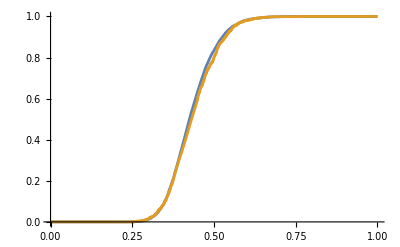

```mathematica
Plot[{CDF[EmpiricalDistribution[testtrials1],x],CDF[EmpiricalDistribution[testtrials2],x]},{x,0,1},PlotRange->All]
```

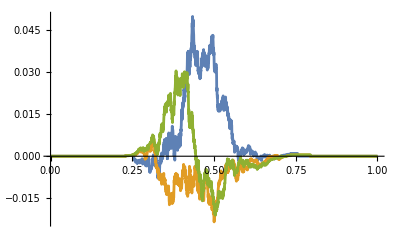

```mathematica
Plot[{CDF[EmpiricalDistribution[testtrials1],x]-CDF[EmpiricalDistribution[testtrials2],x],CDF[EmpiricalDistribution[testtrials1],x]-CDF[EmpiricalDistribution[testtrials3],x],CDF[EmpiricalDistribution[testtrials1],x]-CDF[EmpiricalDistribution[testtrials4],x]},{x,0,1},PlotRange->All]
```

### Femur data

```mathematica
AbsoluteTiming[femurhopkinsnulltrials = Map[Flatten,ParallelTable[With[{testd = makechrandsold[femursets2[[i]]]},Table[hopkins[testd,hfrac],{20}]],{i,1,Length[femursets2]},{100}]];]
```

{3.00431,Null}

```mathematica
Dimensions[femurhopkinsnulltrials]
```

{4,2000}

```mathematica
femurhopkinschnulltrials =  Map[Flatten,ParallelTable[With[{testd = makechrandsold[femursets2[[i]]]},Table[hopkinsch[testd,hfrac],{20}]],{i,1,Length[flens]},{100}]];
```

```mathematica
femurlawsonjursnulltrials =  Map[Flatten,ParallelTable[With[{testd = makechrandsold[femursets2[[i]]]},Table[lawsonjurs[testd,hfrac],{20}]],{i,1,Length[flens]},{100}]];
```

```mathematica
(*femureds =Map[EmpiricalDistribution[Flatten[#]]&,{femurhopkinsnulltrials,femurhopkinschnulltrials,femurlawsonjursnulltrials}];*)
```

```mathematica
femureds = Transpose[{Map[EmpiricalDistribution,femurhopkinsnulltrials],Map[EmpiricalDistribution,femurhopkinschnulltrials],Map[EmpiricalDistribution,femurlawsonjursnulltrials]}];
```

```mathematica
femurhds =Map[HistogramDistribution[Flatten[#],{0.01}]&,{femurhopkinsnulltrials,femurhopkinschnulltrials,femurlawsonjursnulltrials}];
```

```mathematica
Dimensions[femureds]
```

{4,3}

```mathematica
fs2len = Map[Length,femursets2]
```

{58,59,58,59}

```mathematica
betas = Map[BetaDistribution[#,#]&,fs2len]
```

{BetaDistribution[58,58],BetaDistribution[59,59],BetaDistribution[58,58],BetaDistribution[59,59]}

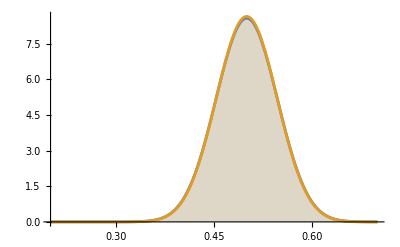

```mathematica
Plot[{PDF[betas[[1]],x],PDF[betas[[2]],x]},{x,0.2,0.7},PlotPoints->100,PlotRange->All,Filling->Axis,Exclusions->Null]
```

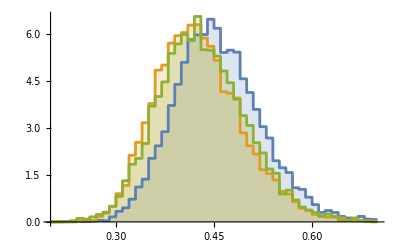

```mathematica
Plot[{PDF[femurhds[[1]],x],PDF[femurhds[[2]],x],PDF[femurhds[[3]],x]},{x,0.2,0.7},PlotPoints->100,PlotRange->All,Filling->Axis,Exclusions->Null]
```

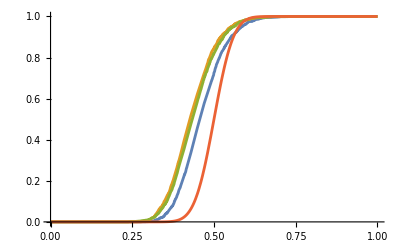

```mathematica
Plot[{CDF[femureds[[1,1]],x],CDF[femureds[[1,2]],x],CDF[femureds[[1,3]],x],CDF[betas[[1]],x]},{x,0,1},PlotRange->All]
```

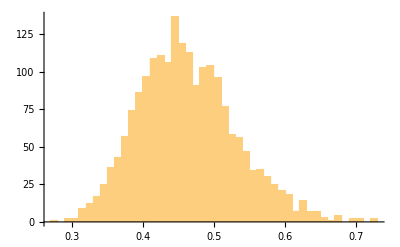

```mathematica
Histogram[femurhopkinsnulltrials[[1]],{.01}]
```

```mathematica
femurhopstats = ParallelMap[{hopkins[#,hfrac],hopkinsch[#,hfrac],lawsonjurs[#,hfrac]}&,femursets2]
```

{{0.414021,0.429688,0.515432},{0.439292,0.307906,0.447511},{0.395981,0.525483,0.350822},{0.338871,0.379566,0.326065}}

```mathematica
hoppvalue[femureds[[1,3]],femurhopstats[[1,3]]]
```

0.266

```mathematica
hopkinpvaluesfemur = Table[hoppvalue[femureds[[i,j]],femurhopstats[[i,j]]],{i,1,Length[femurhopstats]},{j,1,3}]
```

{{0.497,0.961,0.266},{0.968,0.052,0.698},{0.366,0.171,0.186},{0.048,0.512,0.099}}

```mathematica
ribhopstats = ParallelMap[{hopkins[#,hfrac],hopkinsch[#,hfrac],lawsonjurs[#,hfrac]}&,ribsets2]
```

{{0.404067,0.487811,0.440757},{0.491048,0.308465,0.456839},{0.412353,0.452337,0.334849},{0.517243,0.339123,0.392731}}

```mathematica
(*hopkinpvaluesrib = Table[hoppvalue[ribeds[[i,j]],ribhopstats[[i,j]]],{i,1,Length[ribhopstats]},{j,1,3}]*)
```

```mathematica
Map[Flatten,Transpose[{femursetnames2,hopkinpvaluesfemur}]]//TableForm
```

F0D0 | 0.497 | 0.961 | 0.266
F0D2 | 0.968 | 0.052 | 0.698
F0D0: lam = 0.06 | 0.366 | 0.171 | 0.186
F0D2, lam = 0.06 | 0.048 | 0.512 | 0.099

```mathematica
(*Map[Flatten,Transpose[{ribsetnames2,ribsrt,hopkinpvaluesrib}]]//TableForm*)
```

#### Running Hopkins multiple times

```mathematica
AbsoluteTiming[hptm = hopkinstest[femursets2[[1]],hopkins,0.2,100,100,100];]
```

{0.906242,Null}

```mathematica
hptm
```

{0.453941,0.9318}

#### Integrated test

```mathematica
AbsoluteTiming[hpt = hopkinstest[femursets2[[1]],hopkins,0.2,100,100,100];]
```

{0.948907,Null}

```mathematica
hpt
```

{0.449629,0.8694}

```mathematica
AbsoluteTiming[femurhoptests = Table[{hopkinstest[femursets2[[i]],hopkins,0.2,100,100,100],hopkinstest[femursets2[[i]],hopkinsch,0.2,100,100,100],hopkinstest[femursets2[[i]],lawsonjurs,0.2,100,100,100]},{i,1,Length[femursets2]}];]
```

{52.1172,Null}

```mathematica
AbsoluteTiming[ribhoptests = Table[{hopkinstest[ribsets2[[i]],hopkins,0.2,100,100,100],hopkinstest[ribsets2[[i]],hopkinsch,0.2,100,100,100],hopkinstest[ribsets2[[i]],lawsonjurs,0.2,100,100,100]},{i,1,Length[ribsets2]}];]
```

{53.9007,Null}

```mathematica
tabhead = {"Data set","H orig","p-value","H fpm","p-value","H lj","p-value"};
```

```mathematica
Join[{tabhead},Map[Flatten,Transpose[{femursetnames2,femurhoptests}]]]//TableForm
```

Data set | H orig | p-value | H fpm | p-value | H lj | p-value
F0D0 | 0.445241 | 0.84 | 0.41724 | 0.8762 | 0.42753 | 0.9024
F0D2 | 0.472865 | 0.6714 | 0.420517 | 0.9898 | 0.399561 | 0.7578
F0D0: lam = 0.06 | 0.459255 | 0.9054 | 0.42748 | 0.973 | 0.421205 | 0.8886
F0D2, lam = 0.06 | 0.473911 | 0.8692 | 0.417509 | 0.9334 | 0.378924 | 0.4254

```mathematica
Join[{tabhead},Map[Flatten,Transpose[{ribsetnames2,ribhoptests}]]]//TableForm
```

Data set | H orig | p-value | H fpm | p-value | H lj | p-value
F0D0 | 0.453808 | 0.9994 | 0.432043 | 0.9734 | 0.428584 | 0.9954
F0D2 | 0.449403 | 0.8922 | 0.403995 | 0.8632 | 0.419447 | 0.9908
F0D0: lam = 0.07 | 0.44655 | 0.7864 | 0.428066 | 0.9876 | 0.424459 | 0.8296
F0D2, lam = 0.07 | 0.431565 | 0.8412 | 0.406847 | 0.8874 | 0.40842 | 0.7972

## Variance

```mathematica
fvsets = Join[Partition[femursets2,2],{fdiscbyclasscentered}];
```

```mathematica
fvsets[[1]]
```

{{{1.03222,0.541},{0.920123,0.471},{0.298853,0.464},{0.745075,0.353},{1.46864,0.403},{0.999565,0.489},{1.23553,0.559},{0.824776,0.403},{0.833784,0.421},{0.911158,0.514},{0.127105,0.355},{1.50651,0.759},{1.0086,0.791},{2.23553,0.773},{2.01953,0.772},{2.2188,0.855},{0.982271,0.544},{1.01703,0.533},{1.0607,0.631},{1.96661,0.82},{1.78675,0.766},{1.86747,0.723},{1.48144,0.463},{1.53403,0.545},{1.58995,0.632},{1.74507,0.576},{1.41162,0.55},{1.78462,0.511},{1.45025,0.457},{1.15534,0.479},{1.65418,0.6},{1.3483,0.641},{1.20683,0.451},{1.6721,0.73},{1.3784,0.697},{1.80346,0.545},{1.1038,0.66},{1.3032,0.647},{0.908485,0.631},{0.968483,0.656},{0.586587,0.778},{0.184691,0.679},{0.559907,0.436},{0.30103,0.481},{1.89454,0.749},{1.41996,0.589},{0.807535,0.731},{-0.0357404,0.761},{0.130334,0.689},{0.587711,0.75},{0.367356,0.77},{0.184691,0.632},{0.853698,0.7},{0.729165,0.482},{1.07078,0.692},{0.658011,0.8},{0.429752,0.572},{0.181844,0.574}},{{1.25527,0.884},{1,0.901},{1.21471,0.864},{1.34163,0.926},{1.10116,0.929},{1.41263,0.733},{0.89487,0.968},{1.09304,0.952},{1.21125,0.874},{1.92469,0.97},{1.0983,0.635},{1.3601,0.725},{2.21864,0.776},{1.93692,0.659},{0.871573,0.867},{1.22386,0.988},{1.4609,0.729},{1.4833,0.985},{1.4375,0.828},{1.3075,0.973},{1.28103,0.968},{0.713323,0.955},{0.909823,0.938},{0.737511,0.909},{1.42844,0.738},{1.20656,0.828},{1.33646,0.776},{1.34792,0.821},{0.93044,0.792},{0.956649,0.939},{0.966611,0.623},{1.46982,0.966},{1.44028,0.845},{1.3216,0.859},{1.36884,0.959},{1.61278,0.9},{1.00732,0.673},{0.97174,0.843},{1.55291,0.765},{1.5563,0.936},{1.42915,0.893},{0.681241,0.989},{1.36116,0.865},{1.35984,0.764},{0.975753,0.942},{0.906335,0.872},{1.52114,0.687},{1.57978,0.596},{1.4624,0.749},{1.47392,0.767},{1.84136,0.726},{1.77335,0.828},{0.679428,0.849},{0.70757,0.89},{1.00087,0.85},{0.363612,0.844},{-0.0136762,0.729},{0.716838,0.871},{0.733999,0.689}}}

```mathematica
femurvet = VarianceEquivalenceTest[fdiscbyclasscentered,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
ribvet = VarianceEquivalenceTest[rdiscbyclasscentered,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
femurvet["TestDataTable",{"BrownForsythe","Conover","Levene"}]
```

| Statistic | P-Value
Brown-Forsythe | 5.29316 | 0.0232117
Conover | 2.33821 | 0.0193765
Levene | 5.18783 | 0.0245934

```mathematica
ribvet["TestDataTable",{"BrownForsythe","Conover","Levene"}]
```

| Statistic | P-Value
Brown-Forsythe | 7.62504 | 0.00675639
Conover | -2.67815 | 0.00740306
Levene | 9.70682 | 0.00234672